# Steady state rotating disk electrode voltammetry

## Fully implicit scheme

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
FrameTicks->Automatic,
GridLines->None,
ImagePadding->{{Inherited,5},{Inherited,5}},
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
optionA={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameLabel-> {
Style["increment",FontFamily-> "Arial" ,FontSize->  12,FontColor->Black],
Style["χ",FontFamily->  "Times New Roman" ,FontSize->   12, FontWeight->   "Plain",FontColor-> Black],
None,
None}
};
```

```mathematica
optionB={
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12,FontColor->Black, FontSlant->Italic],
Style["χ",FontFamily-> "Times New Roman",FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
cvTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];

cvTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],5}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],1}]];

cvTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeRDESSDiagonals];

makeRDESSDiagonals[m_Integer][zMax_]:=Module[{x,y,z},
x=Table[1.-(2.13496*zMax^3*(j-1)^2)/(2.*(m-1)^3),{j,3,m-1}];
z=Table[1.+(2.13496*zMax^3*(j-1)^2)/(2.*(m-1)^3),{j,2,m-2}];
y=Table[-2.,{j,2,m-1}];
{x,y,z}]
```

```mathematica
Clear[zMax,x,y,z];
{x,y,z}=makeRDESSDiagonals[7][zMax]
```

{{1.-0.0197681 zMax^3,1.-0.0444783 zMax^3,1.-0.0790726 zMax^3,1.-0.123551 zMax^3},{-2.,-2.,-2.,-2.,-2.},{1.+0.00494204 zMax^3,1.+0.0197681 zMax^3,1.+0.0444783 zMax^3,1.+0.0790726 zMax^3}}

```mathematica
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},5]//MatrixForm
```

(-2. | 1.+0.00494204 zMax^3 | 0 | 0 | 0
1.-0.0197681 zMax^3 | -2. | 1.+0.0197681 zMax^3 | 0 | 0
0 | 1.-0.0444783 zMax^3 | -2. | 1.+0.0444783 zMax^3 | 0
0 | 0 | 1.-0.0790726 zMax^3 | -2. | 1.+0.0790726 zMax^3
0 | 0 | 0 | 1.-0.123551 zMax^3 | -2.)

## Set Up Solution

```mathematica
Clear[implicitSolveRDESS];

implicitSolveRDESS[m_Integer,n_Integer,{lowerLimit_,upperLimit_},{ksStar_,α_,zMax_}]:=Module[{x,y,z,len,mat,x1,y1,z1,initial,range,τ,solveNext,zM},

range=(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeRDESSDiagonals[m][zMax];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
x1=1-(2.13496*zMax^3)/(2.*(m-1)^3);
y1=y⟦1⟧;
z1=z⟦1⟧;
zM=1.+(2.13496*zMax^3*(j-1)^2)/(2.*(m-1)^3)/.j-> (m-1);

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2},
ξ=Exp[upperLimit-(τ*(k-1))];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));
b=ConstantArray[0.,{m-2}];
b⟦1⟧-=(tmp*x1*ksStar*ξ^(1.-α));
b⟦-1⟧-=zM;
mat⟦1,1⟧=y1+4.*x1*tmp;
mat⟦1,2⟧=z1-x1*tmp;
tmp2=LinearSolve[mat,b];
Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]];

Rest@FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)

f=F/(R*T);
```

### Electrochemical variables

```mathematica
Clear[α,upperLimit,lowerLimit,𝕥];

α=0.5 (*transfer coefficient*);

lowerLimit=-10.(*limit = f×(E-E^o)*);

upperLimit=10.(*limit = f×(E-E^o)*);

𝕥=upperLimit+Abs[lowerLimit];
```

### Simulation variables

```mathematica
Clear[n,τ,m,zMax,Δz,ksDim,ksStar];

n=200;

τ=𝕥/(n-1);(*calculation of the incremental time/potential step*)

m=100;

zMax=2.;
Δz=zMax/(m-1);

ksDim=2000.;

ksStar=2.*ksDim*zMax/(m-1);
```

## Solve

```mathematica
c=implicitSolveRDESS[m,n,{lowerLimit,upperLimit},{ksStar,α,zMax}];
```

## Plot RDE voltammogram

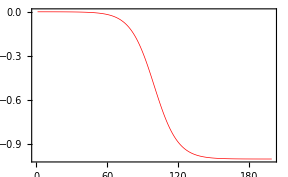

```mathematica
rde=Map[((3*#⟦1⟧-4*#⟦2⟧+#⟦3⟧)*(m-1)/(2.*zMax))&,c];
plot1=ListPlot[rde]
```

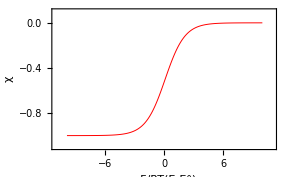

```mathematica
rde2=Table[{upperLimit-((j-1)*τ),rde⟦j⟧},{j,1,Length[rde]}];

plot2=ListPlot[rde2,optionB,PlotRange->{{upperLimit+1,lowerLimit-1},{-1.1,0.1}}]
```